# Make a Maxwell-Boltzmann distribution of the kappa dists

Data options

```mathematica
binSize=0.5;
EarlyOrLate="Late";
BeamNoBeam="Beam";
```

### Setup data generated on 2018/05/09

```mathematica
Switch[binSize,
0.5,
kHistEarlyReq={{1.70,8.00},{2.20,65.00},{2.70,134.00},{3.20,183.00},{3.70,142.00},{4.20,148.00},{4.70,137.00},{5.20,160.00},{5.70,113.00},{6.20,93.00},{6.70,69.00},{7.20,77.00},{7.70,63.00},{8.20,64.00},{8.70,38.00},{9.20,37.00},{9.70,29.00},{10.20,28.00},{10.70,25.00},{11.20,25.00},{11.70,29.00},{12.20,12.00},{12.70,19.00},{13.20,12.00},{13.70,8.00},{14.20,10.00},{14.70,8.00},{15.20,8.00},{15.70,5.00},{16.20,12.00},{16.70,5.00},{17.20,7.00},{17.70,10.00},{18.20,3.00},{18.70,8.00},{19.20,5.00},{19.70,4.00},{20.20,2.00},{20.70,6.00},{21.20,1.00},{21.70,5.00},{22.20,5.00},{22.70,1.00},{23.20,1.00},{23.70,4.00},{24.20,1.00},{24.70,3.00},{25.20,1.00},{25.70,3.00},{26.20,2.00},{26.70,3.00},{27.20,2.00},{27.70,0.00},{28.20,5.00},{28.70,0.00},{29.20,1.00},{29.70,0.00},{30.20,3.00},{30.70,1.00},{31.20,0.00},{31.70,0.00},{32.20,2.00},{32.70,1.00},{33.20,0.00},{33.70,3.00},{34.20,0.00},{34.70,0.00},{35.20,1.00},{35.70,0.00},{36.20,0.00},{36.70,1.00},{37.20,0.00},{37.70,0.00},{38.20,0.00},{38.70,0.00},{39.20,0.00},{39.70,1.00},{40.20,1.00},{40.70,0.00},{41.20,0.00},{41.70,0.00},{42.20,1.00},{42.70,1.00},{43.20,1.00},{43.70,1.00},{44.20,0.00},{44.70,0.00},{45.20,0.00},{45.70,1.00},{46.20,1.00},{46.70,1.00},{47.20,1.00},{47.70,0.00},{48.20,0.00},{48.70,0.00},{49.20,0.00},{49.70,0.00},{50.20,0.00},{50.70,0.00},{51.20,1.00},{51.70,0.00},{52.20,1.00},{52.70,0.00},{53.20,0.00},{53.70,0.00},{54.20,1.00},{54.70,0.00},{55.20,0.00},{55.70,0.00},{56.20,1.00},{56.70,0.00},{57.20,0.00},{57.70,0.00},{58.20,0.00},{58.70,0.00},{59.20,0.00},{59.70,0.00},{60.20,0.00},{60.70,0.00},{61.20,0.00},{61.70,0.00},{62.20,0.00},{62.70,0.00},{63.20,0.00},{63.70,0.00},{64.20,0.00},{64.70,0.00},{65.20,0.00},{65.70,0.00},{66.20,0.00},{66.70,1.00}};
kHistEarlyExc={{1.70,109.00},{2.20,372.00},{2.70,714.00},{3.20,787.00},{3.70,891.00},{4.20,922.00},{4.70,862.00},{5.20,763.00},{5.70,695.00},{6.20,596.00},{6.70,557.00},{7.20,511.00},{7.70,427.00},{8.20,336.00},{8.70,313.00},{9.20,264.00},{9.70,242.00},{10.20,203.00},{10.70,188.00},{11.20,147.00},{11.70,129.00},{12.20,107.00},{12.70,110.00},{13.20,93.00},{13.70,82.00},{14.20,75.00},{14.70,72.00},{15.20,69.00},{15.70,65.00},{16.20,57.00},{16.70,49.00},{17.20,56.00},{17.70,43.00},{18.20,42.00},{18.70,42.00},{19.20,27.00},{19.70,25.00},{20.20,28.00},{20.70,40.00},{21.20,20.00},{21.70,24.00},{22.20,27.00},{22.70,21.00},{23.20,15.00},{23.70,16.00},{24.20,17.00},{24.70,25.00},{25.20,19.00},{25.70,17.00},{26.20,15.00},{26.70,17.00},{27.20,17.00},{27.70,15.00},{28.20,15.00},{28.70,7.00},{29.20,12.00},{29.70,10.00},{30.20,12.00},{30.70,9.00},{31.20,8.00},{31.70,9.00},{32.20,10.00},{32.70,10.00},{33.20,5.00},{33.70,13.00},{34.20,6.00},{34.70,9.00},{35.20,2.00},{35.70,6.00},{36.20,5.00},{36.70,4.00},{37.20,7.00},{37.70,7.00},{38.20,7.00},{38.70,5.00},{39.20,4.00},{39.70,2.00},{40.20,1.00},{40.70,2.00},{41.20,8.00},{41.70,4.00},{42.20,1.00},{42.70,3.00},{43.20,2.00},{43.70,2.00},{44.20,1.00},{44.70,3.00},{45.20,2.00},{45.70,1.00},{46.20,1.00},{46.70,3.00},{47.20,3.00},{47.70,1.00},{48.20,2.00},{48.70,1.00},{49.20,4.00},{49.70,0.00},{50.20,0.00},{50.70,2.00},{51.20,0.00},{51.70,1.00},{52.20,0.00},{52.70,4.00},{53.20,6.00},{53.70,2.00},{54.20,2.00},{54.70,4.00},{55.20,0.00},{55.70,2.00},{56.20,0.00},{56.70,1.00},{57.20,0.00},{57.70,1.00},{58.20,2.00},{58.70,1.00},{59.20,0.00},{59.70,0.00},{60.20,1.00},{60.70,4.00},{61.20,1.00},{61.70,0.00},{62.20,0.00},{62.70,1.00},{63.20,0.00},{63.70,1.00},{64.20,0.00},{64.70,0.00},{65.20,0.00},{65.70,1.00},{66.20,0.00},{66.70,2.00},{67.20,1.00},{67.70,0.00},{68.20,0.00},{68.70,2.00},{69.20,0.00},{69.70,2.00},{70.20,0.00},{70.70,0.00},{71.20,0.00},{71.70,0.00},{72.20,1.00},{72.70,0.00},{73.20,1.00},{73.70,0.00},{74.20,1.00},{74.70,0.00},{75.20,0.00},{75.70,0.00},{76.20,0.00},{76.70,0.00},{77.20,1.00},{77.70,0.00},{78.20,0.00},{78.70,1.00},{79.20,1.00},{79.70,2.00},{80.20,0.00},{80.70,0.00},{81.20,0.00},{81.70,0.00},{82.20,0.00},{82.70,0.00},{83.20,0.00},{83.70,0.00},{84.20,0.00},{84.70,0.00},{85.20,0.00},{85.70,0.00},{86.20,0.00},{86.70,0.00},{87.20,0.00},{87.70,0.00},{88.20,0.00},{88.70,0.00},{89.20,0.00},{89.70,1.00},{90.20,0.00},{90.70,0.00},{91.20,0.00},{91.70,0.00},{92.20,0.00},{92.70,0.00},{93.20,0.00},{93.70,0.00},{94.20,0.00},{94.70,1.00}};
kHistLateReq={{1.70,1.00},{2.20,11.00},{2.70,55.00},{3.20,74.00},{3.70,72.00},{4.20,106.00},{4.70,105.00},{5.20,97.00},{5.70,102.00},{6.20,88.00},{6.70,64.00},{7.20,67.00},{7.70,54.00},{8.20,47.00},{8.70,55.00},{9.20,33.00},{9.70,44.00},{10.20,40.00},{10.70,24.00},{11.20,23.00},{11.70,21.00},{12.20,25.00},{12.70,27.00},{13.20,15.00},{13.70,11.00},{14.20,11.00},{14.70,16.00},{15.20,12.00},{15.70,12.00},{16.20,6.00},{16.70,7.00},{17.20,9.00},{17.70,8.00},{18.20,7.00},{18.70,7.00},{19.20,3.00},{19.70,4.00},{20.20,3.00},{20.70,8.00},{21.20,6.00},{21.70,5.00},{22.20,5.00},{22.70,4.00},{23.20,2.00},{23.70,3.00},{24.20,4.00},{24.70,7.00},{25.20,1.00},{25.70,4.00},{26.20,1.00},{26.70,6.00},{27.20,2.00},{27.70,2.00},{28.20,3.00},{28.70,3.00},{29.20,1.00},{29.70,1.00},{30.20,2.00},{30.70,2.00},{31.20,0.00},{31.70,5.00},{32.20,1.00},{32.70,2.00},{33.20,2.00},{33.70,0.00},{34.20,2.00},{34.70,0.00},{35.20,2.00},{35.70,1.00},{36.20,0.00},{36.70,0.00},{37.20,1.00},{37.70,3.00},{38.20,1.00},{38.70,1.00},{39.20,0.00},{39.70,1.00},{40.20,0.00},{40.70,2.00},{41.20,0.00},{41.70,0.00},{42.20,0.00},{42.70,0.00},{43.20,0.00},{43.70,2.00},{44.20,0.00},{44.70,1.00},{45.20,0.00},{45.70,0.00},{46.20,0.00},{46.70,0.00},{47.20,0.00},{47.70,1.00},{48.20,0.00},{48.70,1.00},{49.20,0.00},{49.70,0.00},{50.20,1.00},{50.70,0.00},{51.20,1.00},{51.70,0.00},{52.20,0.00},{52.70,0.00},{53.20,1.00},{53.70,0.00},{54.20,0.00},{54.70,2.00},{55.20,0.00},{55.70,0.00},{56.20,0.00},{56.70,0.00},{57.20,0.00},{57.70,0.00},{58.20,0.00},{58.70,0.00},{59.20,0.00},{59.70,2.00},{60.20,0.00},{60.70,0.00},{61.20,1.00},{61.70,0.00},{62.20,0.00},{62.70,0.00},{63.20,0.00},{63.70,0.00},{64.20,0.00},{64.70,0.00},{65.20,0.00},{65.70,0.00},{66.20,0.00},{66.70,0.00},{67.20,1.00},{67.70,0.00},{68.20,0.00},{68.70,0.00},{69.20,0.00},{69.70,0.00},{70.20,0.00},{70.70,0.00},{71.20,1.00}};
kHistLateExc={{1.70,44.00},{2.20,132.00},{2.70,207.00},{3.20,322.00},{3.70,418.00},{4.20,453.00},{4.70,514.00},{5.20,519.00},{5.70,496.00},{6.20,449.00},{6.70,448.00},{7.20,391.00},{7.70,353.00},{8.20,302.00},{8.70,235.00},{9.20,224.00},{9.70,204.00},{10.20,179.00},{10.70,171.00},{11.20,140.00},{11.70,113.00},{12.20,123.00},{12.70,99.00},{13.20,87.00},{13.70,76.00},{14.20,74.00},{14.70,78.00},{15.20,68.00},{15.70,69.00},{16.20,52.00},{16.70,42.00},{17.20,50.00},{17.70,57.00},{18.20,51.00},{18.70,25.00},{19.20,34.00},{19.70,35.00},{20.20,26.00},{20.70,29.00},{21.20,35.00},{21.70,24.00},{22.20,32.00},{22.70,26.00},{23.20,22.00},{23.70,24.00},{24.20,13.00},{24.70,18.00},{25.20,16.00},{25.70,21.00},{26.20,14.00},{26.70,12.00},{27.20,14.00},{27.70,15.00},{28.20,17.00},{28.70,21.00},{29.20,13.00},{29.70,16.00},{30.20,14.00},{30.70,11.00},{31.20,5.00},{31.70,12.00},{32.20,6.00},{32.70,8.00},{33.20,9.00},{33.70,13.00},{34.20,8.00},{34.70,6.00},{35.20,7.00},{35.70,5.00},{36.20,5.00},{36.70,13.00},{37.20,6.00},{37.70,7.00},{38.20,6.00},{38.70,6.00},{39.20,7.00},{39.70,5.00},{40.20,4.00},{40.70,4.00},{41.20,4.00},{41.70,4.00},{42.20,5.00},{42.70,8.00},{43.20,5.00},{43.70,1.00},{44.20,6.00},{44.70,4.00},{45.20,3.00},{45.70,4.00},{46.20,1.00},{46.70,5.00},{47.20,2.00},{47.70,5.00},{48.20,3.00},{48.70,3.00},{49.20,2.00},{49.70,0.00},{50.20,1.00},{50.70,1.00},{51.20,2.00},{51.70,0.00},{52.20,0.00},{52.70,0.00},{53.20,3.00},{53.70,3.00},{54.20,3.00},{54.70,3.00},{55.20,0.00},{55.70,0.00},{56.20,4.00},{56.70,0.00},{57.20,1.00},{57.70,6.00},{58.20,1.00},{58.70,3.00},{59.20,0.00},{59.70,2.00},{60.20,0.00},{60.70,1.00},{61.20,0.00},{61.70,0.00},{62.20,0.00},{62.70,0.00},{63.20,2.00},{63.70,3.00},{64.20,1.00},{64.70,0.00},{65.20,0.00},{65.70,0.00},{66.20,0.00},{66.70,1.00},{67.20,0.00},{67.70,2.00},{68.20,1.00},{68.70,0.00},{69.20,1.00},{69.70,0.00},{70.20,1.00},{70.70,1.00},{71.20,0.00},{71.70,1.00},{72.20,0.00},{72.70,0.00},{73.20,1.00},{73.70,0.00},{74.20,1.00},{74.70,0.00},{75.20,1.00},{75.70,0.00},{76.20,0.00},{76.70,1.00},{77.20,0.00},{77.70,1.00},{78.20,0.00},{78.70,0.00},{79.20,0.00},{79.70,0.00},{80.20,0.00},{80.70,0.00},{81.20,0.00},{81.70,0.00},{82.20,0.00},{82.70,0.00},{83.20,0.00},{83.70,0.00},{84.20,0.00},{84.70,0.00},{85.20,1.00},{85.70,0.00},{86.20,0.00},{86.70,0.00},{87.20,0.00},{87.70,0.00},{88.20,0.00},{88.70,0.00},{89.20,0.00},{89.70,1.00},{90.20,0.00},{90.70,0.00},{91.20,1.00},{91.70,0.00},{92.20,0.00},{92.70,0.00},{93.20,0.00},{93.70,0.00},{94.20,0.00},{94.70,0.00},{95.20,0.00},{95.70,0.00},{96.20,0.00},{96.70,0.00},{97.20,0.00},{97.70,0.00},{98.20,0.00},{98.70,0.00},{99.20,0.00},{99.70,0.00},{100.20,4.00}};,
1.0,
kHistEarlyReq={{1.95,73.00},{2.95,317.00},{3.95,290.00},{4.95,297.00},{5.95,206.00},{6.95,146.00},{7.95,127.00},{8.95,75.00},{9.95,57.00},{10.95,50.00},{11.95,41.00},{12.95,31.00},{13.95,18.00},{14.95,16.00},{15.95,17.00},{16.95,12.00},{17.95,13.00},{18.95,13.00},{19.95,6.00},{20.95,7.00},{21.95,10.00},{22.95,2.00},{23.95,5.00},{24.95,4.00},{25.95,5.00},{26.95,5.00},{27.95,5.00},{28.95,1.00},{29.95,3.00},{30.95,1.00},{31.95,2.00},{32.95,1.00},{33.95,3.00},{34.95,1.00},{35.95,0.00},{36.95,1.00},{37.95,0.00},{38.95,0.00},{39.95,2.00},{40.95,0.00},{41.95,1.00},{42.95,2.00},{43.95,1.00},{44.95,0.00},{45.95,2.00},{46.95,2.00},{47.95,0.00},{48.95,0.00},{49.95,0.00},{50.95,1.00},{51.95,1.00},{52.95,0.00},{53.95,1.00},{54.95,0.00},{55.95,1.00},{56.95,0.00},{57.95,0.00},{58.95,0.00},{59.95,0.00},{60.95,0.00},{61.95,0.00},{62.95,0.00},{63.95,0.00},{64.95,0.00},{65.95,0.00},{66.95,1.00}};
kHistEarlyExc={{1.95,481.00},{2.95,1501.00},{3.95,1813.00},{4.95,1625.00},{5.95,1291.00},{6.95,1068.00},{7.95,763.00},{8.95,577.00},{9.95,445.00},{10.95,335.00},{11.95,236.00},{12.95,203.00},{13.95,157.00},{14.95,141.00},{15.95,122.00},{16.95,105.00},{17.95,85.00},{18.95,69.00},{19.95,53.00},{20.95,60.00},{21.95,51.00},{22.95,36.00},{23.95,33.00},{24.95,44.00},{25.95,32.00},{26.95,34.00},{27.95,30.00},{28.95,19.00},{29.95,22.00},{30.95,17.00},{31.95,19.00},{32.95,15.00},{33.95,19.00},{34.95,11.00},{35.95,11.00},{36.95,11.00},{37.95,14.00},{38.95,9.00},{39.95,3.00},{40.95,10.00},{41.95,5.00},{42.95,5.00},{43.95,3.00},{44.95,5.00},{45.95,2.00},{46.95,6.00},{47.95,3.00},{48.95,5.00},{49.95,0.00},{50.95,2.00},{51.95,1.00},{52.95,10.00},{53.95,4.00},{54.95,4.00},{55.95,2.00},{56.95,1.00},{57.95,3.00},{58.95,1.00},{59.95,1.00},{60.95,5.00},{61.95,0.00},{62.95,1.00},{63.95,1.00},{64.95,0.00},{65.95,1.00},{66.95,3.00},{67.95,0.00},{68.95,2.00},{69.95,2.00},{70.95,0.00},{71.95,1.00},{72.95,1.00},{73.95,1.00},{74.95,0.00},{75.95,0.00},{76.95,1.00},{77.95,0.00},{78.95,2.00},{79.95,2.00},{80.95,0.00},{81.95,0.00},{82.95,0.00},{83.95,0.00},{84.95,0.00},{85.95,0.00},{86.95,0.00},{87.95,0.00},{88.95,0.00},{89.95,1.00},{90.95,0.00},{91.95,0.00},{92.95,0.00},{93.95,0.00},{94.95,1.00}};
kHistLateReq={{1.95,12.00},{2.95,129.00},{3.95,178.00},{4.95,202.00},{5.95,190.00},{6.95,131.00},{7.95,101.00},{8.95,88.00},{9.95,84.00},{10.95,47.00},{11.95,46.00},{12.95,42.00},{13.95,22.00},{14.95,28.00},{15.95,18.00},{16.95,16.00},{17.95,15.00},{18.95,10.00},{19.95,7.00},{20.95,14.00},{21.95,10.00},{22.95,6.00},{23.95,7.00},{24.95,8.00},{25.95,5.00},{26.95,8.00},{27.95,5.00},{28.95,4.00},{29.95,3.00},{30.95,2.00},{31.95,6.00},{32.95,4.00},{33.95,2.00},{34.95,2.00},{35.95,1.00},{36.95,1.00},{37.95,4.00},{38.95,1.00},{39.95,1.00},{40.95,2.00},{41.95,0.00},{42.95,0.00},{43.95,2.00},{44.95,1.00},{45.95,0.00},{46.95,0.00},{47.95,1.00},{48.95,1.00},{49.95,1.00},{50.95,1.00},{51.95,0.00},{52.95,1.00},{53.95,0.00},{54.95,2.00},{55.95,0.00},{56.95,0.00},{57.95,0.00},{58.95,0.00},{59.95,2.00},{60.95,1.00},{61.95,0.00},{62.95,0.00},{63.95,0.00},{64.95,0.00},{65.95,0.00},{66.95,1.00},{67.95,0.00},{68.95,0.00},{69.95,0.00},{70.95,1.00}};
kHistLateExc={{1.95,176.00},{2.95,529.00},{3.95,871.00},{4.95,1033.00},{5.95,945.00},{6.95,839.00},{7.95,655.00},{8.95,459.00},{9.95,383.00},{10.95,311.00},{11.95,236.00},{12.95,186.00},{13.95,150.00},{14.95,146.00},{15.95,121.00},{16.95,92.00},{17.95,108.00},{18.95,59.00},{19.95,61.00},{20.95,64.00},{21.95,56.00},{22.95,48.00},{23.95,37.00},{24.95,34.00},{25.95,35.00},{26.95,26.00},{27.95,32.00},{28.95,34.00},{29.95,30.00},{30.95,16.00},{31.95,18.00},{32.95,17.00},{33.95,21.00},{34.95,13.00},{35.95,10.00},{36.95,19.00},{37.95,13.00},{38.95,13.00},{39.95,9.00},{40.95,8.00},{41.95,9.00},{42.95,13.00},{43.95,7.00},{44.95,7.00},{45.95,5.00},{46.95,7.00},{47.95,8.00},{48.95,5.00},{49.95,1.00},{50.95,3.00},{51.95,0.00},{52.95,3.00},{53.95,6.00},{54.95,3.00},{55.95,4.00},{56.95,1.00},{57.95,7.00},{58.95,3.00},{59.95,2.00},{60.95,1.00},{61.95,0.00},{62.95,2.00},{63.95,4.00},{64.95,0.00},{65.95,0.00},{66.95,1.00},{67.95,3.00},{68.95,1.00},{69.95,1.00},{70.95,1.00},{71.95,1.00},{72.95,1.00},{73.95,1.00},{74.95,1.00},{75.95,0.00},{76.95,1.00},{77.95,1.00},{78.95,0.00},{79.95,0.00},{80.95,0.00},{81.95,0.00},{82.95,0.00},{83.95,0.00},{84.95,1.00},{85.95,0.00},{86.95,0.00},{87.95,0.00},{88.95,0.00},{89.95,1.00},{90.95,1.00},{91.95,0.00},{92.95,0.00},{93.95,0.00},{94.95,0.00},{95.95,0.00},{96.95,0.00},{97.95,0.00},{98.95,0.00},{99.95,4.00}};
]
```

```mathematica
Switch[EarlyOrLate,
"Early",
kHistReq=kHistEarlyReq;
kHistExc=kHistEarlyExc;,
"Late",
kHistReq=kHistLateReq;
kHistExc=kHistLateExc;
]
```

```mathematica
Switch[BeamNoBeam,
"Beam",
kHist=kHistReq;,
"NoBeam",
kHist=kHistExc;
]
```

### Plots

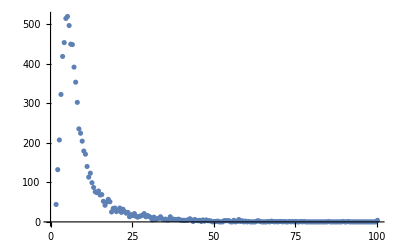

```mathematica
ListPlot[kHist,PlotRange->All]
```

Fit function

### Reduce fit data to those corresponding to κ ≥ ...

```mathematica
fitAboveKappa=1;
fitBelowKappa=15;
```

```mathematica
kapInd=(Position[kHist[[;;,1]],Min[Select[kHist[[;;,1]],# ≥ fitAboveKappa &]]]//Flatten)[[1]];
kapHighInd=(Position[kHist[[;;,1]],Max[Select[kHist[[;;,1]],# ≤  fitBelowKappa &]]]//Flatten)[[1]];
```

```mathematica
fitDat=kHist[[kapInd;;kapHighInd,;;]];
```

## Now the fit

```mathematica
fitFunc=a (x+c)^2 Exp[- b (x+c)^2];
fitParms={a,b,c};
```

```mathematica
spenceRecommends={a->100,b->0.05,c->0};
fitParms={{a,a/.spenceRecommends},{b,b/.spenceRecommends},{c,c/.spenceRecommends}}
```

{{a,100},{b,0.05},{c,0}}

```mathematica
parmVals =FindFit[fitDat,{fitFunc,{a>0.0,b>0.0}},fitParms,x]
```

{a→41.1719,b→0.0310674,c→0.0222053}

```mathematica
fitFunc/.parmVals
```

21.7614 ⅇ^(-0.0521044 (-0.000487096+x)^2) (-0.000487096+x)^2

```mathematica
fitFunc/.parmVals~Join~{x->1.51}
```

89.8586

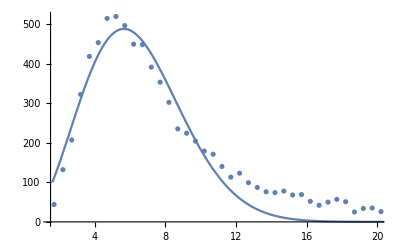

```mathematica
Show[Plot[(fitFunc)/.parmVals,{x,1.6,80},PlotRange->{{1.5,20},All}],ListPlot[kHist]]
```

```mathematica
ListPlot[kHist]
```

```mathematica
Manipulate[Show[Plot[fitFunc/.{a->aVal,b->bVal,c->cVal},{x,1,80},PlotRange->{{1,20},{0,200}}],ListPlot[kHist]],{{aVal,a/.parmVals},0,200},{{bVal,b/.parmVals},0,0.2},{{cVal,c/.parmVals},-1,20}]
```

ListPlot::lpn: kHist is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[kHist]].

ListPlot::lpn: kHist is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[kHist]].

ListPlot::lpn: kHist is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[kHist]].

ListPlot::lpn: kHist is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[kHist]].

## I get it, try a different one

### Works for “Late” “NoBeam” distribution

```mathematica
(*This works for late nobeam distribution
fitFunc=a (x+c)^2 Exp[- b (x+c)^1];
{a->256.2690119446602,b->0.5289275321077902,c->-1.32768230996197}
*)
```

```mathematica
fitFunc=a (x+c)^2 Exp[- b (x+c)^1];
fitParms={a,b,c};
```

```mathematica
spenceRecommends={a->100,b->0.05,c->0};
fitParms={{a,a/.spenceRecommends},{b,b/.spenceRecommends},{c,c/.spenceRecommends}}
```

{{a,100},{b,0.05},{c,0}}

```mathematica
parmVals =FindFit[fitDat,{fitFunc,{a>0.0,b>0.0}},fitParms,x]
```

{a→256.269,b→0.528928,c→-1.32768}

### Press on

```mathematica
fitFunc=a (x+c)^2 Exp[- b (x+c)^0.75];
fitParms={a,b,c};
```

```mathematica
spenceRecommends={a->100,b->0.05,c->0};
fitParms={{a,a/.spenceRecommends},{b,b/.spenceRecommends},{c,c/.spenceRecommends}}
```

{{a,100},{b,0.05},{c,0}}

```mathematica
parmVals =FindFit[fitDat,{fitFunc,{a>0.0,b>0.0,c>-1.5}},fitParms,x]
```

{a→629.18,b→1.08253,c→-1.5}

```mathematica
fitFunc/.parmVals
```

629.18 ⅇ^(-1.08253 (-1.5+x)^0.75) (-1.5+x)^2

```mathematica
fitFunc/.parmVals~Join~{x->1.51}
```

0.0608006

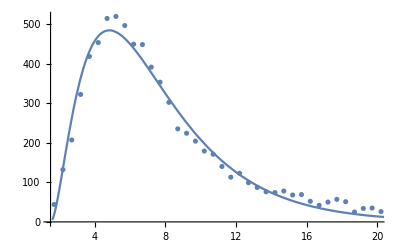

```mathematica
Show[Plot[(fitFunc)/.parmVals,{x,1.6,80},PlotRange->{{1.5,20},All}],ListPlot[kHist]]
```

And again! Log-normal

### Reduce fit data to those corresponding to κ ≥ ...

```mathematica
fitAboveKappa=1;
fitBelowKappa=20;
```

```mathematica
kapInd=(Position[kHist[[;;,1]],Min[Select[kHist[[;;,1]],# ≥ fitAboveKappa &]]]//Flatten)[[1]];
kapHighInd=(Position[kHist[[;;,1]],Max[Select[kHist[[;;,1]],# ≤  fitBelowKappa &]]]//Flatten)[[1]];
```

```mathematica
fitDat=kHist[[kapInd;;kapHighInd,;;]];
```

```mathematica
fitFunc=a PDF[LogNormalDistribution[c,b],x];
fitParms={a,b,c};
```

```mathematica
spenceRecommends={a->100,b->0.05,c->0};
fitParms={{a,a/.spenceRecommends},{b,b/.spenceRecommends},{c,c/.spenceRecommends}}
```

{{a,100},{b,0.05},{c,0}}

```mathematica
parmVals =FindFit[fitDat,{fitFunc,{a>0.01,b>0.001}},fitParms,x]
```

{a→671.936,b→0.498199,c→1.82983}

```mathematica
fitFunc/.parmVals
```

671.936 (Piecewise[{{(0.800768 ⅇ^(-2.01448 (-1.82983+Log[x])^2))/x, x>0}, {0, True}}])

```mathematica
fitFunc/.parmVals~Join~{x->1.51}
```

6.21456

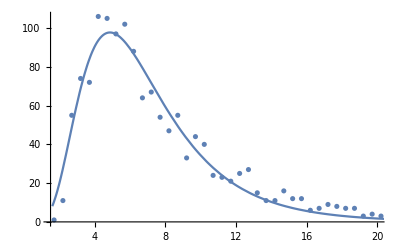

```mathematica
Show[Plot[(fitFunc)/.parmVals,{x,1.6,80},PlotRange->{{1.5,20},All}],ListPlot[kHist]]
```

### Works for “Late” “NoBeam” distribution (NOT EDITABLE)

```mathematica
fitAboveKappa=1;
fitBelowKappa=20;
```

```mathematica
kapInd=(Position[kHist[[;;,1]],Min[Select[kHist[[;;,1]],# ≥ fitAboveKappa &]]]//Flatten)[[1]];
kapHighInd=(Position[kHist[[;;,1]],Max[Select[kHist[[;;,1]],# ≤  fitBelowKappa &]]]//Flatten)[[1]];
```

```mathematica
fitDat=kHist[[kapInd;;kapHighInd,;;]];
```

```mathematica
fitFunc=a PDF[LogNormalDistribution[c,b],x];
fitVars={a,b,c};
```

```mathematica
spenceRecommends={a->100,b->0.05,c->0};
fitVars={{a,a/.spenceRecommends},{b,b/.spenceRecommends},{c,c/.spenceRecommends}}
```

{{a,100},{b,0.05},{c,0}}

```mathematica
fitParms =FindFit[fitDat,{fitFunc,{a>0.01,b>0.001}},fitVars,x]
```

{a→3634.95,b→0.506244,c→1.8778}

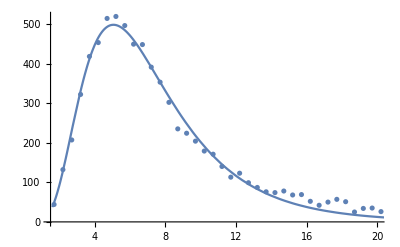

```mathematica
Show[Plot[(fitFunc)/.fitParms,{x,1.6,80},PlotRange->{{1.5,20},All}],ListPlot[kHist]]
```

### Works for “Early” “NoBeam” distribution (NOT EDITABLE)

```mathematica
fitAboveKappa=1;
fitBelowKappa=20;
```

```mathematica
kapInd=(Position[kHist[[;;,1]],Min[Select[kHist[[;;,1]],# ≥ fitAboveKappa &]]]//Flatten)[[1]];
kapHighInd=(Position[kHist[[;;,1]],Max[Select[kHist[[;;,1]],# ≤  fitBelowKappa &]]]//Flatten)[[1]];
```

```mathematica
fitDat=kHist[[kapInd;;kapHighInd,;;]];
```

```mathematica
fitFunc=a PDF[LogNormalDistribution[c,b],x];
fitVars={a,b,c};
```

```mathematica
spenceRecommends={a->100,b->0.05,c->0};
fitVars={{a,a/.spenceRecommends},{b,b/.spenceRecommends},{c,c/.spenceRecommends}}
```

{{a,100},{b,0.05},{c,0}}

```mathematica
fitParms =FindFit[fitDat,{fitFunc,{a>0.01,b>0.001}},fitVars,x]
```

{a→5434.,b→0.520909,c→1.68728}

```mathematica
fitFunc/.fitParms
```

5434. (Piecewise[{{(0.765858 ⅇ^(-1.84266 (-1.68728+Log[x])^2))/x, x>0}, {0, True}}])

```mathematica
fitFunc/.fitParms~Join~{x->1.51}
```

137.728

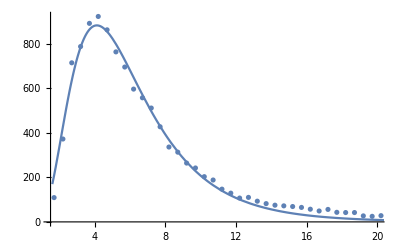

```mathematica
Show[Plot[(fitFunc)/.fitParms,{x,1.6,80},PlotRange->{{1.5,20},All}],ListPlot[kHist]]
```

### Works for “Early” “Beam” distribution (NOT EDITABLE)

```mathematica
fitAboveKappa=1;
fitBelowKappa=20;
```

```mathematica
kapInd=(Position[kHist[[;;,1]],Min[Select[kHist[[;;,1]],# ≥ fitAboveKappa &]]]//Flatten)[[1]];
kapHighInd=(Position[kHist[[;;,1]],Max[Select[kHist[[;;,1]],# ≤  fitBelowKappa &]]]//Flatten)[[1]];
```

```mathematica
fitDat=kHist[[kapInd;;kapHighInd,;;]];
```

```mathematica
fitFunc=a PDF[LogNormalDistribution[c,b],x];
fitVars={a,b,c};
```

```mathematica
spenceRecommends={a->100,b->0.05,c->0};
fitVars={{a,a/.spenceRecommends},{b,b/.spenceRecommends},{c,c/.spenceRecommends}}
```

{{a,100},{b,0.05},{c,0}}

```mathematica
fitParms =FindFit[fitDat,{fitFunc,{a>0.01,b>0.001}},fitVars,x]
```

{a→871.728,b→0.491421,c→1.61095}

```mathematica
fitFunc/.fitParms
```

871.728 (Piecewise[{{(0.811814 ⅇ^(-2.07044 (-1.61095+Log[x])^2))/x, x>0}, {0, True}}])

```mathematica
fitFunc/.fitParms~Join~{x->1.51}
```

23.9084

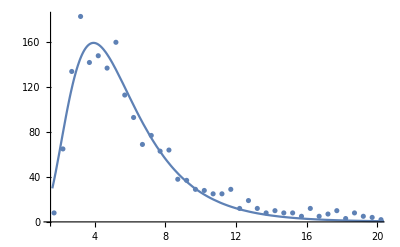

```mathematica
Show[Plot[(fitFunc)/.fitParms,{x,1.6,80},PlotRange->{{1.5,20},All}],ListPlot[kHist]]
```

### Works for “Late” “Beam” distribution (NOT EDITABLE)

```mathematica
fitAboveKappa=1;
fitBelowKappa=20;
```

```mathematica
kapInd=(Position[kHist[[;;,1]],Min[Select[kHist[[;;,1]],# ≥ fitAboveKappa &]]]//Flatten)[[1]];
kapHighInd=(Position[kHist[[;;,1]],Max[Select[kHist[[;;,1]],# ≤  fitBelowKappa &]]]//Flatten)[[1]];
```

```mathematica
fitDat=kHist[[kapInd;;kapHighInd,;;]];
```

```mathematica
fitFunc=a PDF[LogNormalDistribution[c,b],x];
fitVars={a,b,c};
```

```mathematica
spenceRecommends={a->100,b->0.05,c->0};
fitVars={{a,a/.spenceRecommends},{b,b/.spenceRecommends},{c,c/.spenceRecommends}}
```

{{a,100},{b,0.05},{c,0}}

```mathematica
fitParms =FindFit[fitDat,{fitFunc,{a>0.01,b>0.001}},fitVars,x]
```

{a→671.936,b→0.498199,c→1.82983}

```mathematica
fitFunc/.fitParms
```

671.936 (Piecewise[{{(0.800768 ⅇ^(-2.01448 (-1.82983+Log[x])^2))/x, x>0}, {0, True}}])

```mathematica
fitFunc/.fitParms~Join~{x->1.51}
```

6.21456

```mathematica
Show[Plot[(fitFunc)/.fitParms,{x,1.6,80},PlotRange->{{1.5,20},All}],ListPlot[kHist]]
```

-Graphics-